# Black - Scholes Formula

#### By Stephen Palo

## Call Options

A call option is a contract that allows you to buy a certain stock at a maturity time (t) by paying a specified price, called a strike price (K).
If the price of the stock at time t, denoted S(t), is greater than the strike price, you make a profit. If the price of the stock at time t is less than or equal to the strike price, you make nothing.
	Profit = (S(t)-K)^+ = {S(t)-K, if S(t)>K
		  		      = {0	    , if S(t)<K

```mathematica
f[S_,K_]:=If[S-K<0,0,S-K];
Manipulate[Plot[f[S,K],{K,0,100},PlotLabel->Style["(S(t)-K)^+",Blue,Bold,15],AxesLabel->{"K","S"},AspectRatio->1,PlotRange->{-1,100}],{{S,100,"S(t)"},25,100}]
```

## Arbitrage

We define arbitrage as a sure-win betting scheme (i.e. a strategy that guarantees a positive payoff).  
Say C = 3, S(0) = 20, K = 18, t = 1, r = 10%. There is an arbitrage opportunity when you buy the call and short the stock, meaning you receive $20 at t = 0 and deliver the stock at a later time. So you have $17, which you invest at the interest rate of 10% (giving you $18.79 at t=1). If S(1)>18, you exercise the call option and make $0.79 (18.79-18). If S(1)<18, you don’t exercise the call and buy the stock at its market value, so you make more (18.79-S(1)).

```mathematica
up = RandomReal[{18,30}];down = RandomReal[{10,18}];Invested={{0,17},{1,17*Exp[.1]}};StockUp= {{0,20},{1,up}};
StockDown = {{0,20},{1,down}};
Payoff1 = {{0,0},{1,17*Exp[.1]-18}};Payoff2 = {{0,0},{1,17*Exp[.1]-down}};
ListLinePlot[{Invested,StockUp,Payoff1},AxesLabel->{"Time","Money"},PlotLabel->Style["Exercise Call",Blue,Bold,15],PlotLabels->{"Invested Money","Stock Price","Payoff"},ImageSize->Large]ListLinePlot[{Invested,StockDown,Payoff2},AxesLabel->{"Time","Money"},PlotLabel->Style["Do Not Exercise Call",Blue,Bold,15],PlotLabels->{"Invested Money","Stock Price","Payoff"},ImageSize->Large]
```

-Graphics- -Graphics-

## Geometric Brownian Motion

In this model, we assume that the price of the stock evolves with time as a Geometric Brownian Motion (GBM).
We say S(t) is a GBM with drift parameter μ and volatility parameter σ if 
	S(t) = se^(X(t)), 
where s = S(0) and X(t) is a Brownian Motion with mean μ, variance σ^2, and X(0) = 0. This X(t) is a normal random variable with mean μt and variance σ^2t.

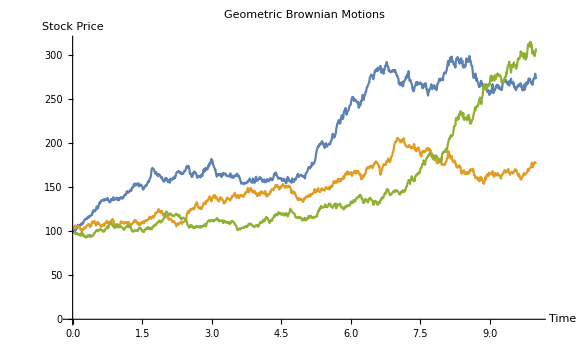

```mathematica
ListLinePlot[Table[RandomFunction[GeometricBrownianMotionProcess[.1,.1,100],{0,10,.01}],{3}],AxesLabel->{"Time","Stock Price"},PlotLabel->"Geometric Brownian Motions",ImageSize->Large]
```

## The Black-Scholes Formula

The Black-Scholes Formula gives us the unique no-arbitrage cost of a call option for a stock that follows Geometric Brownian Motion. It is a function of five variables:
	1. Initial Price of the Stock (s)
	2. Time to Maturity (t)
	3. Strike Price (K)
	4. Volatility (σ)
	5. Interest Rate (r)
We derive the formula from the expected present value of the payoff:
	C_(n-a)(s,t,K,σ,r) = e^-rt E[(S(t)-K)^+]
The formula is:
	C_(n-a)(s,t,K,σ,r) = s ϕ (ω) - Ke^-rtϕ(ω-σt^(1/2)), where 
		ω = (rt+σ^2t/2 -log(K/s))/(σt^(1/2))	and 		ϕ(x) = 1/(2 π)^(1/2)(∫^x)_(-∞)e^(-y^2)ⅆy

## The Black-Scholes Formula

```mathematica
Phi[x_]:=(1/2)*(Erf[x/Sqrt[2]]+1);
Cna[s_,t_,K_,σ_,r_]:= s*Phi[((r+(σ^2)/2)*t-Log[K/s])/(σ*Sqrt[t])]-K*Exp[-r*t]*Phi[((r+(σ^2)/2)*t-Log[K/s])/(σ*Sqrt[t])-σ*Sqrt[t]];
Manipulate[Plot[Cna[s,t,K,σ,r],{s,1,100},PlotLabel->Style["Cost of Call Option",Blue,Bold,15],AxesLabel->{"Stock Price","Option Price"},AspectRatio->1,PlotRange->{0,50},ImageSize->Large],{{t,.5,"Time to Maturity"},.1,1},{{K,100,"Strike Price"},1,150},{{σ,1,"Volatility"},.1,1},{{r,.05,"Interest Rate"},.01,.2},Button["Randomize",{t=RandomReal[{.1,1}],K=RandomReal[{1,150}],σ=RandomReal[{.1,1}],r=RandomReal[{.01,.2}]}]]
```

## Properties of the Black-Scholes Formula

1. C is an increasing, convex function of s
2. C is a decreasing, convex function of K
3. C is increasing in t, σ, and r

∂C/∂s

```mathematica
DS[s_,t_,K_,σ_,r_]:= Phi[((r+(σ^2)/2)*t-Log[K/s])/(σ*Sqrt[t])];
Manipulate[Plot3D[DS[s,t,K,σ,r],{s,-10,100},{t,.1,1},AxesLabel->{"Stock Price","Time to Maturity","Change in Option Price"},PlotLabel->Style["∂C/∂s",Blue,Bold,15],ImageSize->Large],{{K,100,"Strike Price"},1,150},{{σ,1,"Volatility"},.1,1},{{r,.05,"Interest Rate"},.01,.2},Button["Randomize",{K=RandomReal[{1,150}],σ=RandomReal[{.1,1}],r=RandomReal[{.01,.2}]}]]
```

```mathematica
D2S[s_,t_,K_,σ_,r_]:= (Exp[-((((r+(σ^2)/2)*t-Log[K/s])/(σ*Sqrt[t]))^2)/2]/Sqrt[2*Pi])/(s*σ*Sqrt[t]);
Manipulate[Plot3D[D2S[s,t,K,σ,r],{s,-10,100},{t,.1,1},AxesLabel->{"Stock Price","Time to Maturity","Change in Option Price"},PlotLabel->Style["∂^2 C/∂s^2",Blue,Bold,15],ImageSize->Large],{{K,100,"Strike Price"},1,150},{{σ,1,"Volatility"},.1,1},{{r,.05,"Interest Rate"},.01,.2},Button["Randomize",{K=RandomReal[{1,150}],σ=RandomReal[{.1,1}],r=RandomReal[{.01,.2}]}]]
```

∂C/∂K

```mathematica
DK[s_,t_,K_,σ_,r_]:= -Exp[-r*t]*Phi[((r+(σ^2)/2)*t-Log[K/s])/(σ*Sqrt[t])-σ*Sqrt[t]];
Manipulate[Plot3D[DK[s,t,K,σ,r],{K,-10,100},{t,.1,1},AxesLabel->{"Strike Price","Time to Maturity","Change in Option Price"},PlotLabel->Style["∂C/∂K",Blue,Bold,15],ImageSize->Large],{{s,100,"Stock Price"},1,150},{{σ,1,"Volatility"},.1,1},{{r,.05,"Interest Rate"},.01,.2},Button["Randomize",{s=RandomReal[{1,150}],σ=RandomReal[{.1,1}],r=RandomReal[{.01,.2}]}]]
```

```mathematica
D2K[s_,t_,K_,σ_,r_]:= 1/(K*σ*Sqrt[t]);
Manipulate[Plot3D[D2K[s,t,K,σ,r],{K,-10,100},{t,.1,1},AxesLabel->{"Strike Price","Time to Maturity","Change in Option Price"},PlotLabel->Style["∂^2 C/∂K^2",Blue,Bold,15],ImageSize->Large],{{σ,1,"Volatility"},.1,1},Button["Randomize",{s=RandomReal[{1,150}],σ=RandomReal[{.1,1}],r=RandomReal[{.01,.2}]}]]
```

∂C/∂σ

```mathematica
Dσ[s_,t_,K_,σ_,r_]:= s*Sqrt[t]*(Exp[-((((r+(σ^2)/2)*t-Log[K/s])/(σ*Sqrt[t]))^2)/2]/Sqrt[2*Pi]);
Manipulate[Plot3D[Dσ[s,t,K,σ,r],{σ,.1,1},{t,.1,1},AxesLabel->{"Volatility","Time to Maturity","Change in Option Price"},PlotLabel->Style["∂C/∂σ",Blue,Bold,15],ImageSize->Large],{{s,100,"Stock Price"},1,150},{{r,.05,"Interest Rate"},.01,.2},{{K,100,"Strike Price"},1,150},Button["Randomize",{K=RandomReal[{1,150}],s=RandomReal[{1,150}],r=RandomReal[{.01,.2}]}]]
```

```mathematica
D2σ[s_,t_,K_,σ_,r_]:=s*Sqrt[t]*(Exp[-((((r+(σ^2)/2)*t-Log[K/s])/(σ*Sqrt[t]))^2)/2]/Sqrt[2*Pi])*((r+(σ^2)/2)*t-Log[K/s])/(σ*Sqrt[t])*((-r/(Sqrt[t]*σ^2))+Sqrt[t]/2);
Manipulate[Plot3D[D2σ[s,t,K,σ,r],{σ,.1,1},{t,.1,1},AxesLabel->{"Volatility","Time to Maturity","Change in Option Price"},PlotLabel->Style["∂^2 C/∂σ^2",Blue,Bold,15],ImageSize->Large],{{s,100,"Stock Price"},1,150},{{r,.05,"Interest Rate"},.01,.2},{{K,100,"Strike Price"},1,150},Button["Randomize",{K=RandomReal[{1,150}],s=RandomReal[{1,150}],r=RandomReal[{.01,.2}]}]]
```

∂C/∂r

```mathematica
Dr[s_,t_,K_,σ_,r_]:= K*t*Exp[-r*t]*Phi[((r+(σ^2)/2)*t-Log[K/s])/(σ*Sqrt[t])-σ*Sqrt[t]];
Manipulate[Plot3D[Dr[s,t,K,σ,r],{r,.01,.2},{t,.1,1},AxesLabel->{"Interest Rate","Time to Maturity","Change in Option Price"},PlotLabel->Style["∂C/∂r",Blue,Bold,15],ImageSize->Large],{{s,100,"Stock Price"},1,150},{{σ,1,"Volatility"},.1,1},{{K,100,"Strike Price"},1,150},Button["Randomize",{K=RandomReal[{1,150}],σ=RandomReal[{.1,1}],s=RandomReal[{1,150}]}]]
```

∂C/∂t

```mathematica
DCt[s_,t_,K_,σ_,r_]:= (s*σ/(2*Sqrt[t]))*(Exp[-((((r+(σ^2)/2)*t-Log[K/s])/(σ*Sqrt[t]))^2)/2]/Sqrt[2*Pi])+K*r*Exp[-r*t]*Phi[((r+(σ^2)/2)*t-Log[K/s])/(σ*Sqrt[t])-σ*Sqrt[t]];
Manipulate[Plot3D[DCt[s,t,K,σ,r],{s,1,150},{t,.1,1},AxesLabel->{"Stock Price","Time to Maturity","Change in Option Price"},PlotLabel->Style["∂C/∂t",Blue,Bold,15],ImageSize->Large],{{σ,1,"Volatility"},.1,1},{{r,.05,"Interest Rate"},.01,.2},{{K,100,"Strike Price"},1,150},Button["Randomize",{K=RandomReal[{1,150}],σ=RandomReal[{.1,1}],r=RandomReal[{.01,.2}]}]]
```